## Funkcije in odvodi

## Funkcije

Enačbe rešujemo s pomočjo ukaza Solve[ ]. Glej tudi ukaze Roots[ ], NSolve[ ] in FindRoot[ ].

```mathematica
?Solve
?Roots
?NSolve (* Ukaz rešuje numerično *)
?FindRoot (* Ukaz rešuje numerično *)
```

1. Rešite enačbo 2 x^2 + 7x - 15 = 0.

```mathematica
Solve[2x^2+7x-15==0,x]
Roots[2x^2+7x-15==0,x]
NSolve[2x^2+7x-15==0,x]
FindRoot[2x^2+7x-15==0,{x,1}] (* {x,1} to je začetni približek in išče od približka dalje *)
FindRoot[2x^2+7x-15==0,{x,-3}] (* {x,1} to je začetni približek in išče od približka dalje *)
```

{{x→-5},{x→3/2}}

x==3/2||x==-5

{{x→-5.},{x→1.5}}

{x→-5.}

2. Določite ničle polinoma p(x) = x^3 - 3x + 2.
	Rezultati: x_1 = -2, x_(2,3) = 1.

```mathematica
Solve[x^ 3-3x+2 == 0,x]
```

{{x→-2},{x→1},{x→1}}

3. Poiščite ničle, pole, začetno vrednost, poševno asimptoto ter narišite graf racionalne funkcije f(x) = (-6x-x^2+x^3)/(-3+2x+x^2).(ničla = števec 0, pol = imenovalec 0, poševna asimpt: PolynomialQuotient, Plot)
   Rezultati: ničle: x_1 = -2, x_2 = 0, x_3 = 3, poli: x_1 = -3, x_2 = 1, začetna vrednost: f(0) = 0, poševna asimptota: y = x-3.

{{x→-2},{x→0},{x→3}}

{{x→-3},{x→1}}

0

-3+x

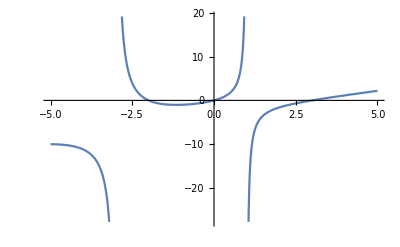

```mathematica
Polinom=(x^ 3-x^ 2-6x)/(x^ 2+2x-3);
Solve[Numerator[Polinom] == 0,x] (* Ničle polinoma *)
Solve[Denominator[Polinom] == 0, x] (* Poli polinoma *)
(* Začetna vrednost*)
Polinom/.x ->0 (* način replace, vse x se zamenja z 0 *)
(* Poševna asimptota*)
PolynomialQuotient[Numerator[Polinom], Denominator[Polinom], x]   
(* Graf polinoma*)
Plot[Polinom, {x, -5,5}]
```

4. Rešite sistem linearnih enačb
		 3x + 3y +  z =  1,
		-4x + 4y + 2z = -4,
		 2x + 3y -  z = -8.
	Rezultati: x = 1, y = -2, z = 4.

```mathematica
EN1=3x+3y+z==1;
EN2=-4x+4y+2z==-4;
EN3=2x+3y-z==-8;

Solve[3x+3y+z==1 && -4x+4y+2z==-4 && 2x+3y-z==-8, {x,y,z} ]
Solve[EN1 && EN2 && EN3, {x,y,z}]
```

{{x→1,y→-2,z→4}}

{{x→1,y→-2,z→4}}

Neenačbe rešujemo s pomočjo ukaza Reduce[ ].

```mathematica
?Reduce
```

5. Določite definicijsko območje funkcije f(x) = √(4 - x^2) + log((x-1)/(x+1)).

-2≤x<-1||1<x≤2

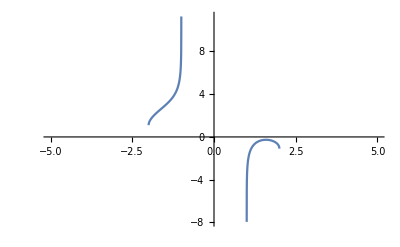

```mathematica
Reduce[{4-x^2≥0,(x-1)/(x+1)>0},x,Reals]
ert = Sqrt[4-x^2]+Log[(x-1)/(x+1)];
Plot[ert ,{x, -5, 5}]
```

6. Rešite kvadratno neenačbo x^2 - 3x - 4 ⩽ 0.
	Rezultat: x ∈ [-1,4].

```mathematica
Reduce[x^ 2-3x-4 ≤0 ]
```

-1≤x≤4

Grafe funkcij rišemo s pomočjo ukaza Plot[ ].

```mathematica
?Plot
```

7. Narišite graf funkcije f(x) = 2 sin(x/2-(2π)/3).

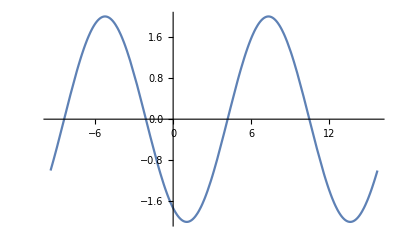

```mathematica
Plot[2Sin[x/2-2Pi/3],{x,-3Pi,5Pi}]
```

Limite funkcij računamo s pomočjo ukaza Limit[ ].

```mathematica
?Limit
```

8. Izračunajte naslednje limite.
	a) lim_(x→0) (sin(3x))/x
	b) lim_(x→∞) (√(x^2 - 1) - x)
	c) lim_(x→4) ((√(1 + 2x) - 3)/(√x - 2))

```mathematica
Limit[Sin[3x]/x,x->0]
Limit[Sqrt[x^2-1]-x,x->Infinity]
Limit[(Sqrt[1+2x]-3)/(Sqrt[x]-2),x->4]
```

3

0

4/3

9. Izračunajte naslednje limite.
	a) lim_(x→0) (1 - cos(x))/x^2 = 1/2
	b) lim_(x→∞) ((x^2 + 1)/(x^2 - 1))^(x^2) = ⅇ^2
	c) lim_(x→1) ((x-1)√(2 - x))/(x^2 - 1)= 1/2

```mathematica
Limit[(1-Cos[x])/x^2, x-> 0]
Limit[((x^ 2+1)/(x^ 2-1))^(x^ 2), x-> Infinity]
Limit[((x-1)Sqrt[2-x])/(x^2-1), x-> 1]
```

1/2

ⅇ^2

1/2

## Odvodi

Odvode funkcij računamo s pomočjo ukaza D[ ].
Izraz poenostavimo s pomočjo ukazov Simplify[ ] ali FullSimplify[ ].

```mathematica
?D
?Simplify
?FullSimplify
```

10. Izračunajte odvode naslednjih funkcij.
	a) f(x) = x √(1 + x^2)
	b) f(x) = (x^2 - 5x - 1)/x^3
	c) f(x) = log^3(x^2)

```mathematica
D[x Sqrt[1+x^2],x]
Simplify[D[x Sqrt[1+x^2],x]]
FullSimplify[D[x Sqrt[1+x^2],x]]

Simplify[D[(x^2-5x-1)/(x^3),x]]
D[Log[x^ 2]^3,x]
```

x^2/(√(1+x^2))+√(1+x^2)

(1+2 x^2)/(√(1+x^2))

(1+2 x^2)/(√(1+x^2))

(3+10 x-x^2)/x^4

(6 Log[x^2]^2)/x

11. Izračunajte prvi in drugi odvod funkcije f(x) = x (sin(ln(x)) + cos(ln(x))).
	Rezultati: f'(x) = 2cos(ln(x)), f''(x) = -(2sin(ln(x)))/x.

```mathematica
(* To nalogo brez resitve! *)
f=x(Sin[Log[x]]+Cos[Log[x]]);
df=D[f,x]
Simplify[df]
D[df,x]
D[D[f,x],x]
D[f,x,x]
D[f,{x,2}]
Simplify[%]
```

Cos[Log[x]]+Sin[Log[x]]+x (Cos[Log[x]]/x-Sin[Log[x]]/x)

2 Cos[Log[x]]

-(2 Sin[Log[x]])/x

-(2 Sin[Log[x]])/x

-(2 Sin[Log[x]])/x

-(2 Cos[Log[x]])/x+2 (Cos[Log[x]]/x-Sin[Log[x]]/x)

-(2 Sin[Log[x]])/x

Ukaz ReplaceAll[ ] nadomesti izraz z vrednostjo. Uporablja se okrajšava /. .
Polinome delimo s pomočjo ukaza PolynomialQuotient[ ].
Ukaz Numerator[ ] vrne števec, ukaz Denominator[ ] pa imenovalec ulomka.

```mathematica
?ReplaceAll
?PolynomialQuotient
?Numerator
?Denominator
```

```mathematica
f=x(Sin[Log[x]]+Cos[Log[x]]);
f/.x->2//N
N[f/.x->2, 11]
```

2.8164

2.8164003554

12. Natančno narišite graf funkcije f(x) = (x^2 + x)/(x + 2).

0

{{x→-1},{x→0}}

{{x→-2}}

0

-1+x

{{x→-2-√2},{x→-2+√2}}

-1

1

-3-2 √2

-3+2 √2

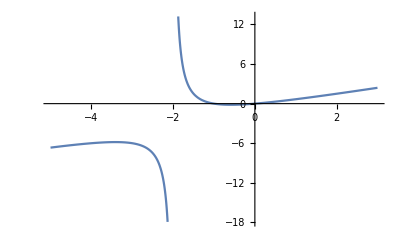

{}

```mathematica
(* še en način za reševanje ničel, ni praktičen *)
g[x_]:=(x^2+x)/(x+2);
g[0]

f=(x^2+x)/(x+2);
(* Ničle: *)
Solve[x^2+x==0,x];
Solve[Numerator[f]==0,x]
(* Poli: *)
Solve[x+2==0,x];
Solve[Denominator[f]==0,x]
(* Začetna vrednost: *)
f/.x->0
(* Poševna asimptota: *)
PolynomialQuotient[x^2+x,x+2,x];
PolynomialQuotient[Numerator[f],Denominator[f],x]
PolynomialRemainder[Numerator[f],Denominator[f],x];
Solve[%==0,x];
Limit[f,x->-Infinity];
Limit[f,x->Infinity];
Limit[f,x->-2,Direction->"FromBelow"];
Limit[f,x->-2,Direction->"FromAbove"];
(* Ekstremi funkcije: *)
Solve[D[f,x]==0,x]
Sign[D[f,x,x]/.x->-2-Sqrt[2]] (* Sign, predznak rezultata *)
Sign[D[f,x,x]/.x->-2+Sqrt[2]]
Simplify[f/.x->-2-Sqrt[2]]
Simplify[f/.x->-2+Sqrt[2]]
(* Graf funkcije: *)
Plot[f,{x,-5,3}]
Plot[f,{x,-5,3},PlotStyle->{Red,Thick}];
Plot[f,{x,-5,3},AspectRatio->Automatic];
(* Prevoji: *)
Solve[D[f,x,x]==0,x]
```

13. Natančno narišite graf funkcije p(x) = x^4 - 2 x^2 - 3.
	Rezultati: ničle: x_1 = -√3, x_2 = √3, začetna vrednost: p(0) = -3, lokalni maksimum pri x_1 = 0, lokalna minimuma pri x_2 = -1 in x_3 = 1.

{{x→-√3},{x→√3}}

-3

∞

∞

{{x→-1},{x→0},{x→1}}

{1,-1,1}

{-4,-3,-4}

-1<x<0||x>1

x<-1||0<x<1

{{x→-0.57735},{x→0.57735}}

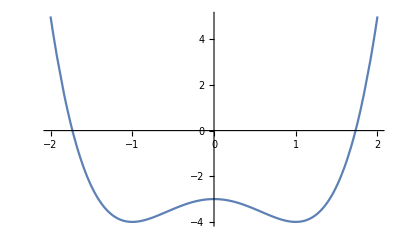

```mathematica
(* To nalogo brez resitve! *)
f=x^4-2x^2-3;
Solve[f==0,x,Reals]  (* ničle *)
f/.x->0                               (* začetna vrednost *)
Limit[f, x -> Infinity] (* limita v +neskončno *)
Limit[f, x -> -Infinity] (* limita v -neskončno *)
Solve[D[f,x]==0,x]      (* stac. točke, so tri *)
Sign[D[f,x,x]/.x->-1]; (* drugi odvod v prvi točki -drugi odvod je poz- lokalni min *)
Sign[D[f,x,x]/.x->0];     (* drugi odvod v drugi točki  -drugi odvod je neg- lokalni max *)
Sign[D[f,x,x]/.x->1];      (* drugi odvod v tretji točki -drugi odvod je poz- lokalni min *)
f/.x->-1;   (* vrednost polinoma v stacionarni točki *)
f/.x->0;   (* vrednost polinoma v stacionarni točki *)
f/.x->1;   (* vrednost polinoma v stacionarni točki *)

Sign[D[f,x,x]/.x->{-1,0,1}]  (* prevoji *)
f/.x->{-1,0,1}
Reduce[D[f,x]>0,x]
Reduce[D[f,x]<0,x]

Solve[D[f,x,x] == 0, x]  // N(* prevoji *)

Plot[f,{x,-2,2}]
```

14. Zapišite enačbo tangente in normale na graf funkcije f(x) = x^3 + 2 x^2 - 4x - 3 v točki T(1,-4).

3

-7+3 x

-1/3

-11/3-x/3

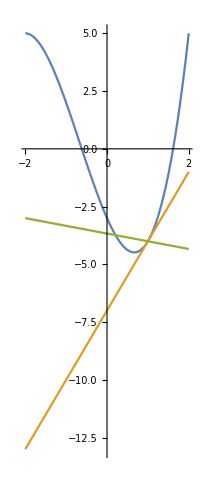

```mathematica
f=x^3+2x^2-4x-3;
x0=1; y0=-4;  (* točka za tangento in normale *)
kt=D[f,x]/.x->x0   (* smerni koef tangente *)
nt=y0-kt*x0;  (* začetna vrednost tangente *)
y=kt*x+nt   (* enačba tangente *)
kn=-1/kt   (* smerni koef normale *)
nn=y0-kn*x0;   (* začetna vrednost normale *)
y=kn*x+nn  (* enačba normale *)
Plot[{f,kt*x+nt,kn*x+nn},{x,-2,2},AspectRatio->Automatic]
```

15. Določite intervale naraščanja in padanja za funkcijo f(x) = (2x)/(1 + x^2).

-1<x<1

x<-1||x>1

-√3<x<0||x>√3

x<-√3||0<x<√3

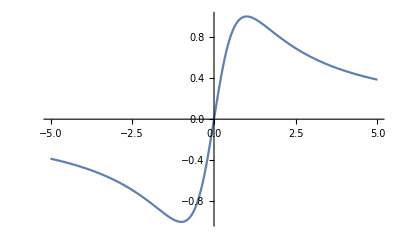

```mathematica
f=2x/(1+x^2);   (*  *)
Reduce[D[f,x]>0,x,Reals] (* f narašča če je f' večji od 0 *)
(* f narašča če je f' manjši od 0 *)
Reduce[D[f,x]<0,x,Reals]

Reduce[D[f,x,x]>0,x,Reals] (* f konveksna če je f'' večji od 0 *)
(* f konkavna če je f'' manjši od 0 *)
Reduce[D[f,x,x]<0,x,Reals]
Plot[f,{x, -5, 5}]
```

16. Določite in klasificirajte lokalne ekstreme funkcije f(x) = x^2 e^-x.

{{x→0},{x→2}}

1

-1

True

True

0.

0.541341

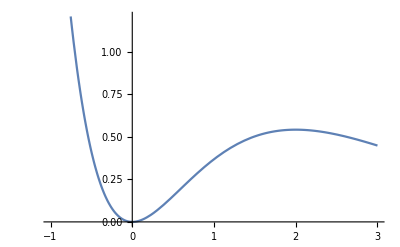

```mathematica
f=x^2 E^(-x);
(* Stacionarne točke: *)
Solve[D[f,x]==0,x]
(* Klasifikacija: *)
Sign[D[f,x,x]/.x->0]
Sign[D[f,x,x]/.x->2]
(* ali *)
(D[f,x,x]/.x->0)>0
(D[f,x,x]/.x->2)<0

(* vrednost funkcije v točkah *)
f/.x->0 //N
f/.x->2 //N
Plot[f, {x, -1, 3}]
```

17. Določite največjo in najmanjšo vrednost funkcije f(x) = (x^2 - 3x)/(x + 1) na intervalu [0,4].
	Rezultati: največja vrednost T_1(4,4/5), najmanša vrednost T_2(1,-1).

{{x→-3},{x→1}}

-1

4/5

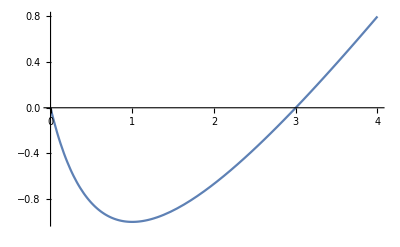

```mathematica
f=(x^2-3x)/(x+1);
a=0; b=4;
Solve[D[f,x]==0,x] (* prvi odvod je 0 v točki 1 *)
f/.x->1   (* vrednost funkcije v točki 1 = -1 *)

f/.x->4  (* vrednost funkcije na koncu intervala *)

Plot[f , {x, 0,4}]
```

```mathematica
(* To nalogo brez resitve! *)
f=(x^2-3x)/(x+1);
a=0; b=4;
x/.Solve[D[f,x]==0,x]
Sign[D[f,x,x]/.x->1]
f/.x->{a,1,b}
Min[%]
Max[%%]
Plot[f,{x,a,b}]
```

{-3,1}

1

{0,-1,4/5}

-1

4/5

-Graphics-